# Testing Wada property for the basins in WeakMagField2\NewBasins

First we import the WadaMergingMethod Package, and the basins

```mathematica
Needs["WadaMergingMethod`"];
SetDirectory[NotebookDirectory[]]
```

E:\Joshua\Documents\Physics\Mathematica notebooks\Research\WeakMagField2\NewBasins

## Near crit ε, positive ℓ (ε=1.2)

```mathematica
files=FileNames["*e(12)pl500.mx"]
```

{b(01)e(12)pl500.mx,b(02)e(12)pl500.mx,b(03)e(12)pl500.mx,b(04)e(12)pl500.mx,b(05)e(12)pl500.mx}

```mathematica
{"b(01)e(12)pl500.mx","b(02)e(12)pl500.mx","b(03)e(12)pl500.mx","b(04)e(12)pl500.mx","b(05)e(12)pl500.mx"}
```

{b(01)e(12)pl500.mx,b(02)e(12)pl500.mx,b(03)e(12)pl500.mx,b(04)e(12)pl500.mx,b(05)e(12)pl500.mx}

```mathematica
AttractorColors={0->White,1->Yellow,2-> Blue,3->Red,4->Black}
```

{0→GrayLevel[1],1→RGBColor[1, 1, 0],2→RGBColor[0, 0, 1],3→RGBColor[1, 0, 0],4→GrayLevel[0],5→RGBColor[0.5, 0, 0.5],6→RGBColor[1, 0.5, 0],7→RGBColor[0, 1, 0],8→GrayLevel[0.5]}

```mathematica
basins=Import[#]&/@files;
```

```mathematica
GraphicsRow[Table[MatrixPlot[basins⟦i⟧,FrameTicks->None,MaxPlotPoints->Infinity,ColorRules->AttractorColors,ImageSize->400],{i,5}]]
```

-Graphics-

```mathematica
numPixels=501^2; (*Total number of pixels in a basin plot*)
```

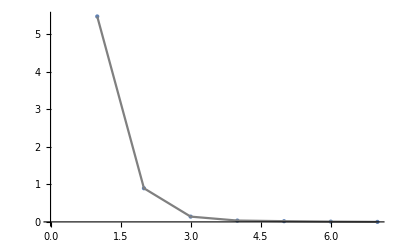

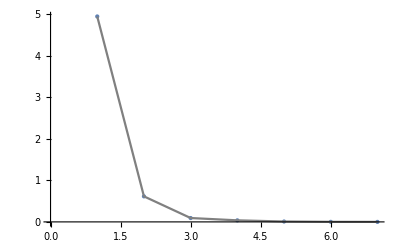

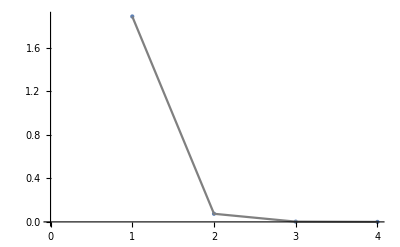

```mathematica
wadaData=Table[testWada[basins⟦i⟧,20],{i,3}];
```

```mathematica
For[i=1,i≤3,i++,wadaData⟦i⟧=wadaData⟦i⟧/.{x_,y_}:>{x,(100*y)/numPixels};]
```

```mathematica
plot1=ListLinePlot[wadaData⟦1⟧,
PlotRange->{All,{0,2}},
PlotStyle->{Blue,Thickness[0.005]},
Frame->True,
GridLines->Automatic,
FrameTicksStyle->Directive[Black,14],
FrameLabel->{Style["Cell["r",ExpressionUUID->"2427289a-a529-4c85-9796-0c44286dd95b"]",Black,Italic,18], Style["% non-Wada points",Black,18]},
ImageSize->400];
```

```mathematica
plot2=ListLinePlot[wadaData⟦2⟧,
PlotRange->{All,{0,2}},
PlotStyle->{Orange,Thickness[0.005]},
Frame->True,
GridLines->Automatic,
FrameTicksStyle->Directive[Black,14],
FrameLabel->{Style["Cell["r",ExpressionUUID->"d1ab2452-e51e-4c7b-8a5a-3932e097b1c9"]",Black,Italic,18], Style["% non-Wada points",Black,18]},
ImageSize->400];
```

```mathematica
plot3=ListLinePlot[wadaData⟦3⟧,
PlotRange->{All,{0,2}},
PlotStyle->{Darker[Green],Thickness[0.005]},
Frame->True,
GridLines->Automatic,
FrameTicksStyle->Directive[Black,14],
FrameLabel->{Style["Cell["r",ExpressionUUID->"0d9cfee0-9aeb-40aa-882f-7ccc63d6f564"]",Black,Italic,18], Style["% non-Wada points",Black,18]},
ImageSize->400];
```

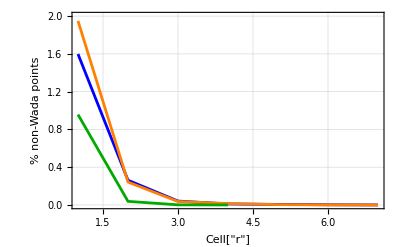

```mathematica
Show[{plot1,plot2,plot3},
Epilog-> Inset[Framed[Column[{
LineLegend[{Blue},{Style["Cell["b = 0.1",ExpressionUUID->"21eb2371-b997-4477-be54-8f3fe8e7b96a"]",Italic,14]}],
LineLegend[{Orange},{Style["Cell["b = 0.2",ExpressionUUID->"c27afec1-63d6-4422-b0df-8e8ac4dc8327"]",Italic,14]}],
LineLegend[{Darker[Green]},{Style["Cell["b = 0.3",ExpressionUUID->"17d1fd83-d6c0-4324-a44c-aca874096313"]",Italic,14]}],
}
],
RoundingRadius->10,
Background->White
],
{6,1.4}
]]
```

## Near crit ε, negative ℓ (ε=ε_crit+0.2)

```mathematica
files=FileNames["*ecritnl500.mx"]
```

{b(01)ecritnl500.mx,b(02)ecritnl500.mx,b(03)ecritnl500.mx,b(04)ecritnl500.mx,b(05)ecritnl500.mx}

```mathematica
AttractorColors={0->White,1->Yellow,2-> Blue,3->Red,4->Black}
```

{0→GrayLevel[1],1→RGBColor[1, 1, 0],2→RGBColor[0, 0, 1],3→RGBColor[1, 0, 0],4→GrayLevel[0]}

```mathematica
basins=Import[#]&/@files;
```

```mathematica
GraphicsRow[Table[MatrixPlot[basins⟦i⟧,FrameTicks->None,MaxPlotPoints->Infinity,ColorRules->AttractorColors,ImageSize->400],{i,5}]]
```

-Graphics-

```mathematica
numPixels=501^2; (*Total number of pixels in a basin plot*)
```

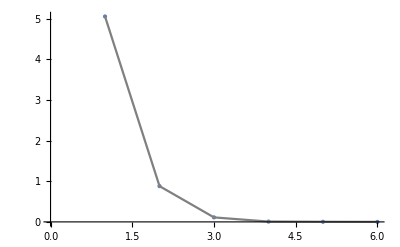

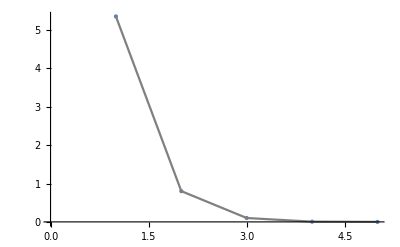

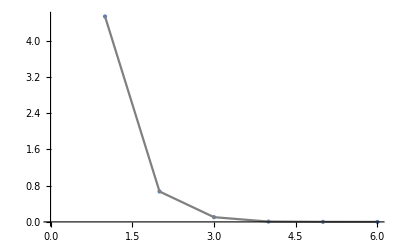

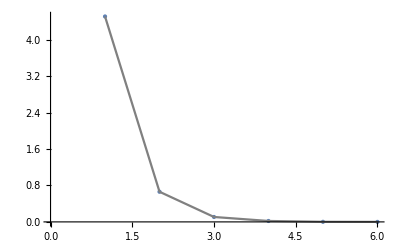

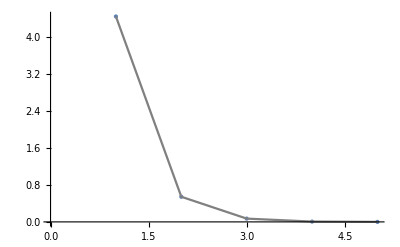

{217.613,Null}

```mathematica
wadaData=Table[testWada[basins⟦i⟧,20],{i,5}];//AbsoluteTiming
```

```mathematica
For[i=1,i≤5,i++,wadaData⟦i⟧=wadaData⟦i⟧/.{x_,y_}:>{x,(100*y)/numPixels};]
```

```mathematica
plot1=ListLinePlot[wadaData⟦1⟧,
PlotRange->{All,{0,2.5}},
PlotStyle->{Blue,Thickness[0.005]},
Frame->True,
GridLines->Automatic,
FrameTicksStyle->Directive[Black,14],
FrameLabel->{Style["Cell["r",ExpressionUUID->"634bc525-91b3-43ea-8bd6-c7f101c8ffce"]",Black,Italic,18], Style["% non-Wada points",Black,18]},
ImageSize->400];
```

```mathematica
plot2=ListLinePlot[wadaData⟦2⟧,
PlotRange->{All,{0,2.5}},
PlotStyle->{Orange,Thickness[0.005]},
Frame->True,
GridLines->Automatic,
FrameTicksStyle->Directive[Black,14],
FrameLabel->{Style["Cell["r",ExpressionUUID->"c0688317-0e3c-46ad-980e-44878166cd1b"]",Black,Italic,18], Style["% non-Wada points",Black,18]},
ImageSize->400];
```

```mathematica
plot3=ListLinePlot[wadaData⟦3⟧,
PlotRange->{All,{0,2.5}},
PlotStyle->{Red,Thickness[0.005]},
Frame->True,
GridLines->Automatic,
FrameTicksStyle->Directive[Black,14],
FrameLabel->{Style["Cell["r",ExpressionUUID->"204dd99c-461d-4d56-85ae-8c97947795b3"]",Black,Italic,18], Style["% non-Wada points",Black,18]},
ImageSize->400];
```

```mathematica
plot4=ListLinePlot[wadaData⟦4⟧,
PlotRange->{All,{0,2.5}},
PlotStyle->{Darker[Green],Thickness[0.005]},
Frame->True,
GridLines->Automatic,
FrameTicksStyle->Directive[Black,14],
FrameLabel->{Style["Cell["r",ExpressionUUID->"72d7cab9-b679-426e-b934-ab8cd595e95c"]",Black,Italic,18], Style["% non-Wada points",Black,18]},
ImageSize->400];
```

```mathematica
plot5=ListLinePlot[wadaData⟦5⟧,
PlotRange->{All,{0,2.5}},
PlotStyle->{Purple,Thickness[0.005]},
Frame->True,
GridLines->Automatic,
FrameTicksStyle->Directive[Black,14],
FrameLabel->{Style["Cell["r",ExpressionUUID->"4eb15c30-b3db-446e-8e2f-463924344ca2"]",Black,Italic,18], Style["% non-Wada points",Black,18]},
ImageSize->400];
```

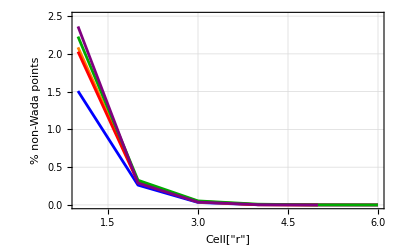

```mathematica
Show[{plot1,plot2,plot3,plot4,plot5},
Epilog-> Inset[Framed[Column[{
LineLegend[{Blue},{Style["Cell["b = 0.1",ExpressionUUID->"a6ebcee0-4a8b-4a21-b469-e0694e14d81c"]",Italic,14]}],
LineLegend[{Orange},{Style["Cell["b = 0.2",ExpressionUUID->"dc99fc4a-c09e-4021-ae3e-c58c01e9b8a9"]",Italic,14]}],
LineLegend[{Red},{Style["Cell["b = 0.3",ExpressionUUID->"82b1e7b4-43e8-4551-a116-ede407723aaa"]",Italic,14]}],
LineLegend[{Darker[Green]},{Style["Cell["b = 0.4",ExpressionUUID->"af0a2fdd-23ce-4f86-8794-e8ad55225680"]",Italic,14]}],
LineLegend[{Purple},{Style["Cell["b = 0.5",ExpressionUUID->"8a156624-11be-427e-8438-13e88d432b6d"]",Italic,14]}]
}
],
RoundingRadius->10,
Background->White
],
{5.3,1.5}
]]
```

## Far crit ε, positive ℓ (ε=3.0)

```mathematica
files=FileNames["*e(30)pl500.mx"]
```

{b(01)e(30)pl500.mx,b(02)e(30)pl500.mx,b(03)e(30)pl500.mx,b(04)e(30)pl500.mx,b(05)e(30)pl500.mx}

```mathematica
AttractorColors={0->White,1->Yellow,2-> Blue,3->Red,4->Black}
```

{0→GrayLevel[1],1→RGBColor[1, 1, 0],2→RGBColor[0, 0, 1],3→RGBColor[1, 0, 0],4→GrayLevel[0]}

```mathematica
basins=Import[#]&/@files;
```

```mathematica
GraphicsRow[Table[MatrixPlot[basins⟦i⟧,FrameTicks->None,MaxPlotPoints->Infinity,ColorRules->AttractorColors,ImageSize->400],{i,5}]]
```

-Graphics-

```mathematica
numPixels=501^2; (*Total number of pixels in a basin plot*)
```

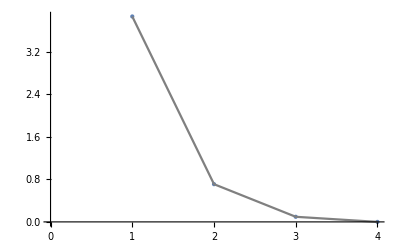

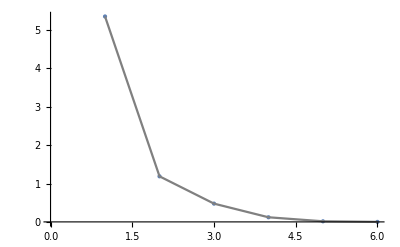

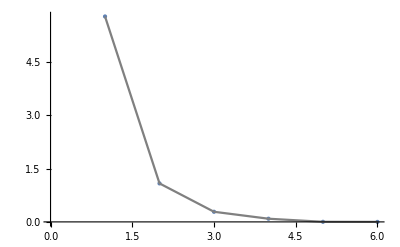

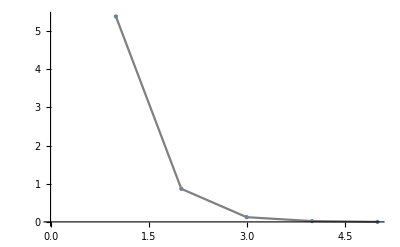

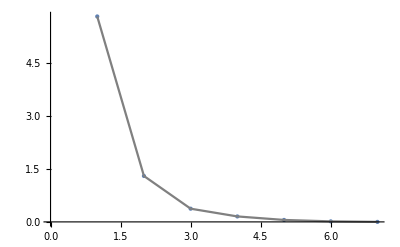

{168.675,Null}

```mathematica
wadaData=Table[testWada[basins⟦i⟧,20],{i,5}];//AbsoluteTiming
```

```mathematica
For[i=1,i≤5,i++,wadaData⟦i⟧=wadaData⟦i⟧/.{x_,y_}:>{x,(100*y)/numPixels};]
```

```mathematica
plot1=ListLinePlot[wadaData⟦1⟧,
PlotRange->{All,{0,1.3}},
PlotStyle->{Blue,Thickness[0.005]},
Frame->True,
GridLines->Automatic,
FrameTicksStyle->Directive[Black,14],
FrameLabel->{Style["Cell["r",ExpressionUUID->"093c5c10-388f-4fbd-a714-008f8893005c"]",Black,Italic,18], Style["% non-Wada points",Black,18]},
ImageSize->400];
```

```mathematica
plot2=ListLinePlot[wadaData⟦2⟧,
PlotRange->{All,{0,1.3}},
PlotStyle->{Orange,Thickness[0.005]},
Frame->True,
GridLines->Automatic,
FrameTicksStyle->Directive[Black,14],
FrameLabel->{Style["Cell["r",ExpressionUUID->"1d0ed0e8-68bb-4e8f-9edc-69394056962d"]",Black,Italic,18], Style["% non-Wada points",Black,18]},
ImageSize->400];
```

```mathematica
plot3=ListLinePlot[wadaData⟦3⟧,
PlotRange->{All,{0,1.3}},
PlotStyle->{Red,Thickness[0.005]},
Frame->True,
GridLines->Automatic,
FrameTicksStyle->Directive[Black,14],
FrameLabel->{Style["Cell["r",ExpressionUUID->"ca5d34f4-2621-4cfb-8d0f-78bb2be51e69"]",Black,Italic,18], Style["% non-Wada points",Black,18]},
ImageSize->400];
```

```mathematica
plot4=ListLinePlot[wadaData⟦4⟧,
PlotRange->{All,{0,1.3}},
PlotStyle->{Darker[Green],Thickness[0.005]},
Frame->True,
GridLines->Automatic,
FrameTicksStyle->Directive[Black,14],
FrameLabel->{Style["Cell["r",ExpressionUUID->"e4e8a9b1-1f9d-4dfb-b585-c09aa15499c6"]",Black,Italic,18], Style["% non-Wada points",Black,18]},
ImageSize->400];
```

```mathematica
plot5=ListLinePlot[wadaData⟦5⟧,
PlotRange->{All,{0,1.3}},
PlotStyle->{Purple,Thickness[0.005]},
Frame->True,
GridLines->Automatic,
FrameTicksStyle->Directive[Black,14],
FrameLabel->{Style["Cell["r",ExpressionUUID->"e1d263b8-a813-4522-ac3f-e4303889f5c9"]",Black,Italic,18], Style["% non-Wada points",Black,18]},
ImageSize->400];
```

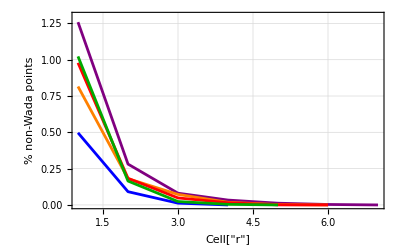

```mathematica
Show[{plot5,plot1,plot2,plot3,plot4},
Epilog-> Inset[Framed[Column[{
LineLegend[{Blue},{Style["Cell["b = 0.1",ExpressionUUID->"33d012b9-cfbc-4e0c-a5f2-0bd0e28cecc1"]",Italic,14]}],
LineLegend[{Orange},{Style["Cell["b = 0.2",ExpressionUUID->"444b1afc-b4b0-4d62-adb9-fcc2461cc9ce"]",Italic,14]}],
LineLegend[{Red},{Style["Cell["b = 0.3",ExpressionUUID->"503e7a7f-c182-4dd8-9928-f185a12235d1"]",Italic,14]}],
LineLegend[{Darker[Green]},{Style["Cell["b = 0.4",ExpressionUUID->"0a20a867-881c-4440-9cdd-785cd1b2e5c7"]",Italic,14]}],
LineLegend[{Purple},{Style["Cell["b = 0.5",ExpressionUUID->"1173f7fc-0cf7-428d-9c24-a14d7e59699e"]",Italic,14]}]
}
],
RoundingRadius->10,
Background->White
],
{6.2,0.77}
]]
```

## Far crit ε, negative ℓ (ε=ε_crit+2.0)

```mathematica
files=FileNames["*e(crit_plus_20)nl500.mx"]
```

{b(01)e(crit_plus_20)nl500.mx,b(02)e(crit_plus_20)nl500.mx,b(03)e(crit_plus_20)nl500.mx,b(04)e(crit_plus_20)nl500.mx,b(05)e(crit_plus_20)nl500.mx}

```mathematica
AttractorColors={0->White,1->Yellow,2-> Blue,3->Red,4->Black}
```

{0→GrayLevel[1],1→RGBColor[1, 1, 0],2→RGBColor[0, 0, 1],3→RGBColor[1, 0, 0],4→GrayLevel[0]}

```mathematica
basins=Import[#]&/@files;
```

```mathematica
GraphicsRow[Table[MatrixPlot[basins⟦i⟧,FrameTicks->None,MaxPlotPoints->Infinity,ColorRules->AttractorColors,ImageSize->400],{i,5}]]
```

-Graphics-

```mathematica
numPixels=501^2; (*Total number of pixels in a basin plot*)
```

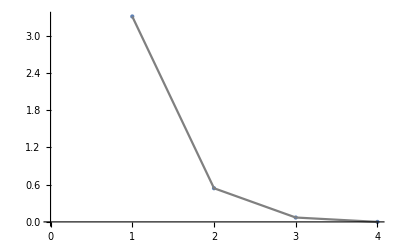

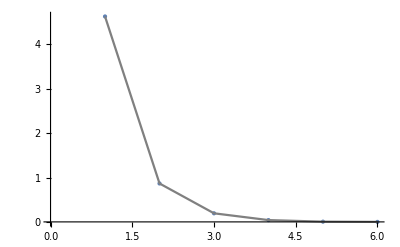

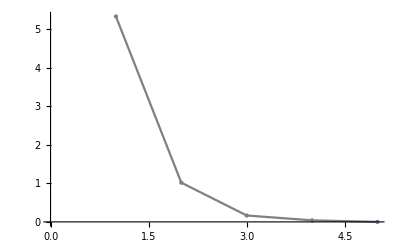

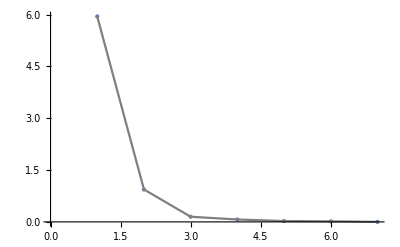

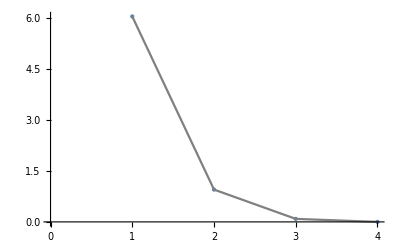

{160.503,Null}

```mathematica
wadaData=Table[testWada[basins⟦i⟧,20],{i,5}];//AbsoluteTiming
```

```mathematica
For[i=1,i≤5,i++,wadaData⟦i⟧=wadaData⟦i⟧/.{x_,y_}:>{x,(100*y)/numPixels};]
```

```mathematica
plot1=ListLinePlot[wadaData⟦1⟧,
PlotRange->{All,{0,1.3}},
PlotStyle->{Blue,Thickness[0.005]},
Frame->True,
GridLines->Automatic,
FrameTicksStyle->Directive[Black,14],
FrameLabel->{Style["Cell["r",ExpressionUUID->"e0a2901d-136b-45db-831d-0dd74acd9719"]",Black,Italic,18], Style["% non-Wada points",Black,18]},
ImageSize->400];
```

```mathematica
plot2=ListLinePlot[wadaData⟦2⟧,
PlotRange->{All,{0,1.3}},
PlotStyle->{Orange,Thickness[0.005]},
Frame->True,
GridLines->Automatic,
FrameTicksStyle->Directive[Black,14],
FrameLabel->{Style["Cell["r",ExpressionUUID->"2d2ab6c5-3a3a-4c94-aa47-9bd393031279"]",Black,Italic,18], Style["% non-Wada points",Black,18]},
ImageSize->400];
```

```mathematica
plot3=ListLinePlot[wadaData⟦3⟧,
PlotRange->{All,{0,1.3}},
PlotStyle->{Red,Thickness[0.005]},
Frame->True,
GridLines->Automatic,
FrameTicksStyle->Directive[Black,14],
FrameLabel->{Style["Cell["r",ExpressionUUID->"ff5421cb-1fdb-43dd-8a1b-06cd9d7c9159"]",Black,Italic,18], Style["% non-Wada points",Black,18]},
ImageSize->400];
```

```mathematica
plot4=ListLinePlot[wadaData⟦4⟧,
PlotRange->{All,{0,1.3}},
PlotStyle->{Darker[Green],Thickness[0.005]},
Frame->True,
GridLines->Automatic,
FrameTicksStyle->Directive[Black,14],
FrameLabel->{Style["Cell["r",ExpressionUUID->"95a478a0-694f-46e8-afe7-6c9f10c488c5"]",Black,Italic,18], Style["% non-Wada points",Black,18]},
ImageSize->400];
```

```mathematica
plot5=ListLinePlot[wadaData⟦5⟧,
PlotRange->{All,{0,1.3}},
PlotStyle->{Purple,Thickness[0.005]},
Frame->True,
GridLines->Automatic,
FrameTicksStyle->Directive[Black,14],
FrameLabel->{Style["Cell["r",ExpressionUUID->"893a84c7-1395-403a-9f03-1346e2058ea8"]",Black,Italic,18], Style["% non-Wada points",Black,18]},
ImageSize->400];
```

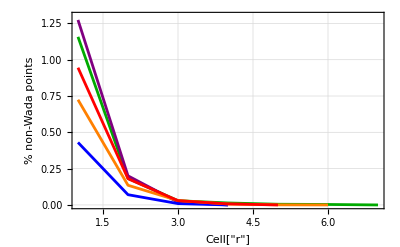

```mathematica
Show[{plot4,plot5,plot1,plot2,plot3},
Epilog-> Inset[Framed[Column[{
LineLegend[{Blue},{Style["Cell["b = 0.1",ExpressionUUID->"87afe490-be1c-4e7b-b9b6-8183f0731f25"]",Italic,14]}],
LineLegend[{Orange},{Style["Cell["b = 0.2",ExpressionUUID->"b9532de6-0634-4188-a726-6452e20cc3db"]",Italic,14]}],
LineLegend[{Red},{Style["Cell["b = 0.3",ExpressionUUID->"dafdd8f7-7a26-4a8a-826a-335eaba9d6c6"]",Italic,14]}],
LineLegend[{Darker[Green]},{Style["Cell["b = 0.4",ExpressionUUID->"020e7068-2fb8-4235-81fb-0f52529564a1"]",Italic,14]}],
LineLegend[{Purple},{Style["Cell["b = 0.5",ExpressionUUID->"3ca09850-04ef-4adc-82ce-ca032354bdc4"]",Italic,14]}]
}
],
RoundingRadius->10,
Background->White
],
{6.2,0.72}
]]
```